## Parámetros

```mathematica
L=8;(* espines *)
```

```mathematica
(* valores para (hz, J) *)
hx=1.;
{hz0,hzf,hzStep}={0.01,3.01,0.5};
{J0,Jf,Jstep}={1.,1.,0.};
hzAndJvalues=Tuples[{Range[hz0,hzf,hzStep],Range[J0,Jf,Jstep]}]
```

{{0.01,1.},{0.51,1.},{1.01,1.},{1.51,1.},{2.01,1.},{2.51,1.},{3.01,1.}}

```mathematica
(* tiempos para la curva de Haar *)
{t0,tf,tStep}={0.,50.,1.};
```

```mathematica
(* Nombre de archivo para guardar el promedio temporal del valor esperado de Haar de la pureza de Choi *)
temporalAvgOfHaarAvgOfChoiPurityFilename="data/temporal_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[NumberForm[L,{Infinity,0}]]<>"_hx_"<>ToString[NumberForm[hx,{Infinity,2}]]<>".csv"
```

data/temporal_haar_avg_choi_purity/wisniacki_open_L_8_hx_1.00.csv

```mathematica
(* número de kernels a usar *)
kernels=24;
```

## Paquetes y definiciones

### Fijar directorio, cargar paquetes y encender kernels

```mathematica
(* Fijar directorio a mis archivos dentro del repositorio *)
SetDirectory[NotebookDirectory[]];

(* Cargar paquetes *)
Get["../Mathematica_packages/QMB.wl"];
```

```mathematica
(* Encender los kernels *)
LaunchKernels[kernels]
```

{Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24),Local (24)}

## Valor esperado de Haar de la pureza de Choi

```mathematica
pauliIndices=Tuples[Range[0,3],L-1];

(* Pauli strings with fixed σ_1 = id *)
pauliStrings=Pauli[Join[{0},#]]&/@pauliIndices;

constants=(1/2)^2*(1/12)^(L-1)*Power[3.,(L-1)-Count[#,x_/;x!=0]]&/@pauliIndices;

(* Lista de tiempos por cada iteración del Do *)
times={};

lenhzAndJvalues = Length[hzAndJvalues];

dimH=2^L;
halfDimH=dimH/2;
halfDimHPlusOne=dimH/2+1;
```

```mathematica
(* Archivo para guardar promedio temporal del valor esperado de Haar de la pureza de Choi *)
dataFile=OpenAppend[temporalAvgOfHaarAvgOfChoiPurityFilename];
WriteString[dataFile,"hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi"<>"\n"];
Close[dataFile];
```

```mathematica
Do[
startTime = AbsoluteTime[];

(* hz y J *)
{hz,J}=hzAndJvalues[[hzAndJ]];

(* Crear Hamiltoniano y diagonalizar *)
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalues, eigenvectors}=Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a la computacional *)
P = Transpose[eigenvectors];

(* Operador de evolución *)
ClearAll[U];U[t_]:=U[t]=P.DiagonalMatrix[Exp[-I*eigenvalues*t]].ConjugateTranspose[P];

(* Calcular valor esperado de Haar de la pureza de Choi para cada t *)
haarAvgChoiPurity = {};
Do[
u=U[t];uDagger=ConjugateTranspose[u];
h=Total[
ParallelTable[
(* Compute partial trace *)
A=#[[1;;halfDimH,1;;halfDimH]]+#[[halfDimHPlusOne;;dimH,halfDimHPlusOne;;dimH]]&[u.pauliStrings[[i]].uDagger,L];
(* Purity *)
Chop[constants[[i]]*Tr[A.A]]
,{i,4^(L-1)}
,DistributedContexts->Full
,ProgressReporting->False]
];
AppendTo[haarAvgChoiPurity,{t,h}]
	,{t,t0,tf,tStep}];

(* Exportar valor esperado de la pureza de Choi para (hz,J) *)
HaarAvgChoiPurityFilename="data/haar_avg_choi_purity/wisniacki/open/L_"<>ToString[NumberForm[L,{Infinity,0}]]<>"/hx_"<>ToString[NumberForm[hx,{Infinity,2}]]<>"_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>".csv";
Export[HaarAvgChoiPurityFilename,Prepend[haarAvgChoiPurity, {"t", "valor esperado de Haar de la pureza de Choi"}], "CSV"];

(* Calcular el promedio temporal de la pureza promedio de Choi *)
fInterp = Interpolation[haarAvgChoiPurity]; 
haarAvgChoiPurityTempAvg = NIntegrate[fInterp[t],{t,t0,tf}]/tf;

(* Agregar {hz, J, haarAvgChoiPurityTempAvg} al archivo CSV *)
dataFile=OpenAppend[temporalAvgOfHaarAvgOfChoiPurityFilename];
WriteString[dataFile,StringJoin[Riffle[ToString/@{hz,J,haarAvgChoiPurityTempAvg},","]]<>"\n"];
Close[dataFile];

endTime = AbsoluteTime[];
time = endTime-startTime;
remainingIterations=(lenhzAndJvalues-hzAndJ);
AppendTo[times,time];
Print[DateString[], ". ",ToString[hzAndJ], "/", lenhzAndJvalues,": ", ToString[NumberForm[time,{Infinity,0}]], " s. Terminará: ", DateString[DatePlus[Now,Quantity[remainingIterations*Mean[times]/3600,"Hours"]]]];

,{hzAndJ,lenhzAndJvalues}];
```

$Aborted

```mathematica
190*30*30/3600.
```

47.5

```mathematica
1/(4*Max[Flatten[Outer[Subtract,#,#]&[eigenvalues]]])
```

0.00880866

```mathematica
eigenvalues//Length
```

128

```mathematica
Range[0,50,0.01]//Length
```

5001

```mathematica
haarChoiPurity=Import["data/haar_avg_choi_purity/wisniacki/open/L_5/hx_1.00_hz_"<>ToString[NumberForm[#,{Infinity,2}]]<>"_J_1.00.csv"][[2;;]]&/@hzAndJvalues[[All,1]];
```

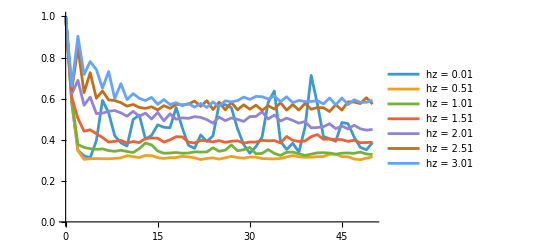

```mathematica
ListPlot[haarChoiPurity,
Joined->True,
PlotRange->Full,
PlotLegends->("hz = "<>ToString[NumberForm[#,{Infinity,2}]]&/@hzAndJvalues[[All,1]])
]
```

## XXZ

```mathematica
?LeaSpinChainHamiltonian
```

```mathematica
L=5;
pauliIndices=Tuples[Range[0,3],L-1];

(* Pauli strings with fixed σ_1 = id *)
pauliStrings=Pauli[Join[{0},#]]&/@pauliIndices;

constants=(1/2)^2*(1/12)^(L-1)*Power[3.,(L-1)-Count[#,x_/;x!=0]]&/@pauliIndices;

(* Lista de tiempos por cada iteración del Do *)
times={};

lenhzAndJvalues = Length[hzAndJvalues];

dimH=2^L;
halfDimH=dimH/2;
halfDimHPlusOne=dimH/2+1;
```

```mathematica
(* Crear Hamiltoniano y diagonalizar *)
H=LeaSpinChainHamiltonian[4.,1.,0.,0.1,L,2];
{eigenvalues, eigenvectors}=Chop[Eigensystem[H]];
```

```mathematica
tStep=1/(4*Max[Flatten[Outer[Subtract,#,#]&[eigenvalues]]])
```

0.0227679

```mathematica
(* Calcular la matriz de cambio de base de la de eigenenergías a la computacional *)
P = Transpose[eigenvectors];

(* Operador de evolución *)
ClearAll[U];U[t_]:=U[t]=P.DiagonalMatrix[Exp[-I*eigenvalues*t]].ConjugateTranspose[P];

(* Calcular valor esperado de Haar de la pureza de Choi para cada t *)
haarAvgChoiPurity = {};
Do[
u=U[t];uDagger=ConjugateTranspose[u];
h=Total[
ParallelTable[
(* Compute partial trace *)
A=#[[1;;halfDimH,1;;halfDimH]]+#[[halfDimHPlusOne;;dimH,halfDimHPlusOne;;dimH]]&[u.pauliStrings[[i]].uDagger,L];
(* Purity *)
Chop[constants[[i]]*Tr[A.A]]
,{i,4^(L-1)}
,DistributedContexts->Full
,ProgressReporting->False]
];
AppendTo[haarAvgChoiPurity,{t,h}]
	,{t,t0,tf,tStep}];

(* Calcular el promedio temporal de la pureza promedio de Choi *)
fInterp = Interpolation[haarAvgChoiPurity]; 
haarAvgChoiPurityTempAvg = NIntegrate[fInterp[t],{t,t0,tf}]/tf;
```

```mathematica
tStep*5
```

0.113839

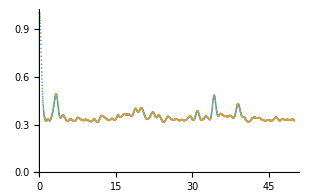

```mathematica
ListPlot[{haarAvgChoiPurity,haarAvgChoiPurity[[1;;-1;;5]]},
Joined->False,
PlotRange->Full
]
```

```mathematica
Mean/@{haarAvgChoiPurity[[All,2]],haarAvgChoiPurity[[1;;-1;;5]][[All,2]]}
```

{0.353815,0.354389}

```mathematica
fInterp = Interpolation[haarAvgChoiPurity]; 
 NIntegrate[fInterp[t],{t,t0,tf}]/tf
```

0.353673

```mathematica
fInterp = Interpolation[haarAvgChoiPurity[[1;;-1;;5]]]; 
 NIntegrate[fInterp[t],{t,t0,49.975478262608995}]/49.975478262608995
```

0.35369

```mathematica
Round[0.35367318788979096,10.^-4]==Round[0.35368980618687273,10.^-4]
```

True